Номер 2
Условие:
Создать таблицу значений функции f(x), разбив отрезок [0; 6]
на n частей неравноотстоящими точками x_i вида (a + b)/2+(b - a)/2*t_i, где t_i – корни многочлена Чебышёва T_(n+1)(t) (i = OverBar[0,n]). Для полученной таблично заданной функции f(x), выполнить следующие действия при n = 6 и n = 10:
а) создать таблицу разделенных разностей функции f(x) по точкам
(x_i, f(x_i)), i = OverBar[0,n];
б) построить интерполяционный многочлен Ньютона Pnr_n(x) для
неравноотстоящих узлов, проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и Pnr_n(x) на одном чертеже);
в) построить интерполирующую функцию Intf_n(x) с помощью функции Interpolation пакета Mathematica, проиллюстрировать графически;
г) вычислить значения функции f(x) и построенных интерполяционных
многочленов Pnr[n](x) и Intf_n(x) в точке x = 2,4316;
д) найти максимумы абсолютных погрешностей интерполирования
функции f(x) многочленом Ньютона Pnr_n(x) и функцией Intf_n(x) на
отрезке [0; 6] с помощью функции FindMaximum пакета Mathematica.

Функция f(x):

```mathematica
f[x_]=3+(2/7 x-Cosh[(3x)/13]) Log[x^2+2 x+3]
```

3+((2 x)/7-Cosh[(3 x)/13]) Log[3+2 x+x^2]

Значения из условия задания:

```mathematica
a=0;b=6;n1=6;n2=10;x0=2.4316;
```

График функции f(x):

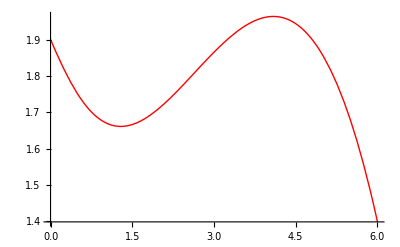

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

Создадим таблицы значений функции для неравноотстоящих узлов на промежутке для n1 = 6 и n2 = 10.

Многочлен Чебышёва для n1 и n2:

```mathematica
T1[i_]=Cos[(Pi (2 i+1))/(2 n1+2)];
```

```mathematica
T2[i_]=Cos[(Pi (2 i+1))/(2 n2+2)];
```

Так как значения корней уменьшаются с увеличением i, полученные таблицы значений функции перевернём с помощью функции Reverse:

```mathematica
data1=Table[{x1=(a+b)/2+(b-a)/2*T1[i],f[x1]},{i,0,n1}]//N//Reverse;
```

```mathematica
data2=Table[{x2=(a+b)/2+(b-a)/2*T2[i],f[x2]},{i,0,n2}]//N//Reverse;
```

```mathematica
{TableForm[data1],TableForm[data2]}
```

{0.0752163 | 1.87519
0.654506 | 1.71762
1.69835 | 1.67981
3. | 1.86632
4.30165 | 1.95989
5.34549 | 1.74546
5.92478 | 1.44772,0.0305357 | 1.89067
0.271104 | 1.81175
0.732751 | 1.70405
1.37808 | 1.66222
2.1548 | 1.73335
3. | 1.86632
3.8452 | 1.95877
4.62192 | 1.93055
5.26725 | 1.77463
5.7289 | 1.56546
5.96946 | 1.41824}

а)

Представим таблицу разделённых разностей функции f(x) в виде матрицы, каждый столбец которой соответствует конечразделённым разностям соответствующего порядка от 0 до n - 1 (разделённые разности 0-го порядка - значения функции в точках  x_i).

Для n = 6:

```mathematica
diftab1=Array[dif1,{n1+1,n1+1},{0,0}];
```

Поскольку с увеличением порядка разделённых разностей их количество уменьшается, заполним пустые клетки таблицы:

```mathematica
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=""]]
```

```mathematica
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]]
```

```mathematica
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++,dif1[i,k]=(dif1[i+1,k-1]-dif1[i,k-1])/(data1[[i+1+k,1]]-data1[[i+1,1]])]]
```

```mathematica
PaddedForm[TableForm[diftab1],{n1,n1-1}]
```

1.87519 | -0.27202 |  0.14528 | -0.02351 | -0.00118 |  0.00037 | -0.00009
 1.71762 | -0.03621 |  0.07653 | -0.02850 |  0.00077 | -0.00013 | 
 1.67981 |  0.14328 | -0.02742 | -0.02490 |  0.00008 |  | 
 1.86632 |  0.07189 | -0.11823 | -0.02457 |  |  | 
 1.95989 | -0.20542 | -0.19010 |  |  |  | 
 1.74546 | -0.51398 |  |  |  |  | 
 1.44772 |  |  |  |  |  |

Аналогичным образом заполним таблицу для n = 10:

```mathematica
diftab2=Array[dif2,{n2+1,n2+1},{0,0}];
```

```mathematica
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]]
```

```mathematica
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]]
```

```mathematica
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=(dif2[i+1,k-1]-dif2[i,k-1])/(data2[[i+1+k,1]]-data2[[i+1,1]])]]
```

```mathematica
PaddedForm[TableForm[diftab2],{n2,n2-1}]
```

1.890665983 | -0.328027336 |  0.134910059 |  0.012819780 | -0.016580323 |  0.004567275 | -0.000911840 |  0.000144698 | -0.000019656 |  2.370873074×10^-6 | -2.594095980×10^-7
 1.811752992 | -0.233291388 |  0.152185248 | -0.022401249 | -0.003017964 |  0.001088915 | -0.000247476 |  0.000041763 | -6.146300945×10^-6 |  8.302579800×10^-7 | 
 1.704054661 | -0.064826345 |  0.109988054 | -0.030636958 |  0.000873919 |  0.000012193 | -0.000038821 |  8.217802929×10^-6 | -1.415191823×10^-6 |  | 
 1.662220517 |  0.091582283 |  0.040526449 | -0.027916933 |  0.000921340 | -0.000163843 |  2.235894785×10^-6 |  8.068494435×10^-7 |  |  | 
 1.733354746 |  0.157313040 | -0.028347978 | -0.024928248 |  0.000284129 | -0.000154115 |  5.940452652×10^-6 |  |  |  | 
 1.866315361 |  0.109393750 | -0.089848962 | -0.024043913 | -0.000266691 | -0.000131454 |  |  |  |  | 
 1.958774704 | -0.036334298 | -0.144362494 | -0.024771686 | -0.000657038 |  |  |  |  |  | 
 1.930552954 | -0.241625134 | -0.191024877 | -0.026167411 |  |  |  |  |  |  | 
 1.774625907 | -0.453084618 | -0.226286559 |  |  |  |  |  |  |  | 
 1.565460634 | -0.611986570 |  |  |  |  |  |  |  |  | 
 1.418236041 |  |  |  |  |  |  |  |  |  |

б)

Построим интерполяционные многочлены Ньютона для неравноотстоящих узлов при n1 = 6 и n2 = 10.

Введём вспомогательные многочлены P(x) и построим интерполяционные многочлены с их помощью:

```mathematica
P1[x_]=1;P2[x_]=1;Pnr1[x_]=dif1[0,0];Pnr2[x_]=dif2[0,0];
```

```mathematica
For[i=0,i<n1,i++,P1[x_]=P1[x] (x-data1[[i+1,1]]);Pnr1[x_]=Pnr1[x]+dif1[0,i+1] P1[x]]
```

```mathematica
Pnr1[x]//Simplify
```

1.90358-0.389276 x+0.156922 x^2+0.0128513 x^3-0.0119771 x^4+0.00166218 x^5-0.0000857078 x^6

```mathematica
For[i=0,i<n2,i++,P2[x_]=P2[x] (x-data2[[i+1,1]]);Pnr2[x_]=Pnr2[x]+dif2[0,i+1] P2[x]]
```

```mathematica
Pnr2[x]//Simplify
```

1.90138-0.352573 x+0.0482871 x^2+0.144693 x^3-0.097417 x^4+0.0351562 x^5-0.00854729 x^6+0.00140688 x^7-0.000150289 x^8+9.38285×10^-6 x^9-2.5941×10^-7 x^10

Изобразим полученные интерполяционные многочлены.

```mathematica
graph1D=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graph2D=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}];
```

Интерполяционный многочлен Ньютона для неравноотстоящих узлов при n = 6:

```mathematica
graph1Pnr=Plot[Pnr1[x],{x,a,b}];
```

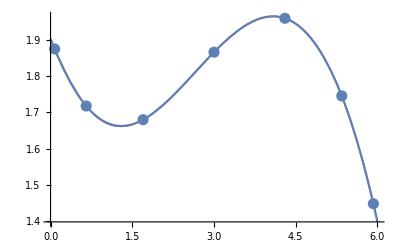

```mathematica
Show[graph,graph1D,graph1Pnr]
```

Интерполяционный многочлен Ньютона для неравноотстоящих узлов при n = 10:

```mathematica
graph2Pnr=Plot[Pnr2[x],{x,a,b}];
```

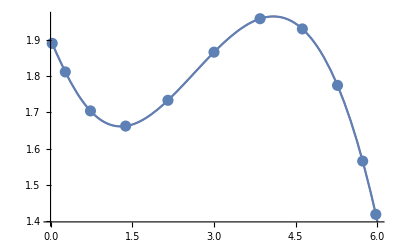

```mathematica
Show[graph,graph2D,graph2Pnr]
```

в)

Интерполирующие функции функции f(x) при n1 = 6 и n2 = 10, построенные встроенной функцией пакета Mathematica:

```mathematica
Intf1=Interpolation[data1]
```

InterpolatingFunction[…]

```mathematica
Intf2=Interpolation[data2]
```

InterpolatingFunction[…]

Изобразим полученные интерполирующие функции.

Интерполирующая функция при n = 6:

```mathematica
graph1Intf=Plot[Intf1[x],{x,a,b}];
```

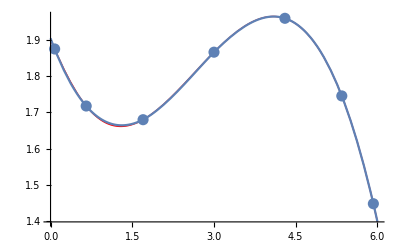

```mathematica
Show[graph,graph1D,graph1Intf]
```

Интерполирующая функция при n = 10:

```mathematica
graph2Intf=Plot[Intf2[x],{x,a,b}];
```

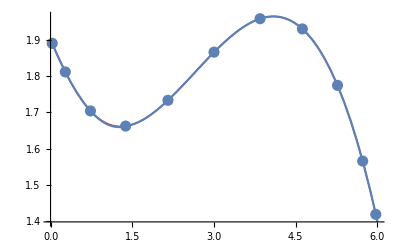

```mathematica
Show[graph,graph2D,graph2Intf]
```

г)

Значения интерполяционных многочленов Ньютона для неравноотстоящих узлов в точке x0:

```mathematica
Print["Pnr1[x0]=",Pnr1[x0],", Pnr2[x0]=",Pnr2[x0]]
```

Pnr1[x0]=1.77448, Pnr2[x0]=1.77543

Значения интерполирующих функций в точке x0:

```mathematica
Print["Intf1[x0]=",Intf1[x0],", Intf2[x0]=",Intf2[x0]]
```

Intf1[x0]=1.77409, Intf2[x0]=1.77515

д)

Исследуем погрешность интерполяционного многочлена Ньютона для неравноотстоящих узлов и интерполирующей функции при n = 6.

```mathematica
Rnp1[x_]=Abs[f[x]-Pnr1[x]]//Simplify;
```

График погрешности Rnp1(x):

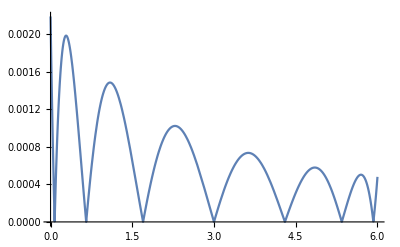

```mathematica
graphErrp1=Plot[Rnp1[x],{x,a,b},PlotRange->Full]
```

Как видно из графика, вблизи левой границы отрезка функция может принимать столь малые значения, их невозможно вычислить машинно, поэтому дадим малое приращение границе а:

```mathematica
maxErrp1=FindMaximum[Rnp1[x],{x,a+0.1,b}]
```

{0.00198711,{x→0.285356}}

Результат, полученный функцией FindMaximum, соответствует графику.

```mathematica
RnI1[x_]=Abs[f[x]-Intf1[x]]//Simplify;
```

График погрешности RnI1(x):

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

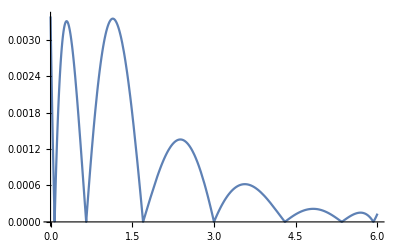

```mathematica
graphErrI1=Plot[RnI1[x],{x,a,b},PlotRange->Full]
```

Как видно из графика, вблизи левой границы отрезка функция может принимать столь малые значения, их невозможно вычислить машинно, поэтому дадим малое приращение границе а:

```mathematica
maxErrI1=FindMaximum[RnI1[x],{x,a+0.1,b}]
```

{0.00330391,{x→0.294864}}

Результат, полученный функцией FindMaximum, соответствует графику.

Аналогимчным образом исследуем погрешность интерполяционного многочлена Ньютона для неравноотстоящих узлов и интерполирующей функции при n = 10.

```mathematica
Rnp2[x_]=Abs[f[x]-Pnr2[x]]//Simplify;
```

График погрешности Rnp2(x):

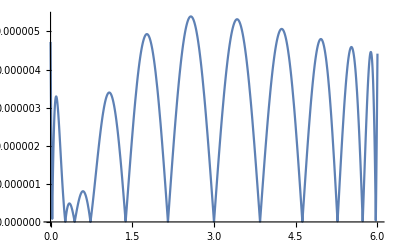

```mathematica
graphErrp2=Plot[Rnp2[x],{x,a,b},PlotRange->Full]
```

Так как в некоторых точках отрезка функия может принимать настолько малые значения, что они не могут быть вычислены машинно, ограничим границы поиска максимума в соответствии с графиком:

```mathematica
maxErrp2=FindMaximum[Rnp2[x],{x,2,4}]
```

{4.93055×10^-6,{x→1.76831}}

```mathematica
RnI2[x_]=Abs[f[x]-Intf2[x]]//Simplify;
```

График погрешности RnI2(x):

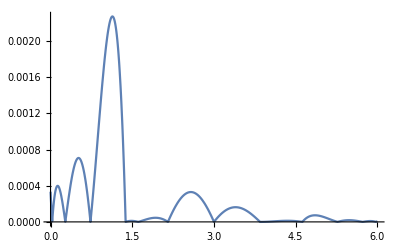

```mathematica
graphErrI2=Plot[RnI2[x],{x,a,b},PlotRange->Full]
```

Как видно из графика, вблизи крайней левой точки отрезка функция погрешности столь малые значения, их невозможно вычислить машинно, следовательно, дадим малое приращение границе a:

```mathematica
maxErrI2=FindMaximum[RnI2[x],{x,0.5,2}]
```

{0.000707388,{x→0.514285}}

Номер 3
Условие:
Сравнить результаты заданий 1 и 2 для равноотстоящих и неравноотстоящих узлов и сделать выводы о зависимости погрешности интерполирования от числа узлов и их расположения на отрезке.

Для наглядности продублируем полученные значения погрешностей.

Погрешности интерполяционного многочлена Ньютона для равноотстоящих узлов при n1 = 6 и n2 = 10:

Погрешности интерполяционного многочлена Ньютона для неравноотстоящих узлов при n1 = 6 и n2 = 10:

Из сравнения результатов вычисления максимальных погрешностей можно сделать вывод о том, что с увеличением количества узлов интерполяции возрастает точность построения интерполяционных многочленов (в обоих случаях значение погрешности при n2 = 10 значительно меньше значения при n1 = 6).
Также из сравнения максимальных погрешностей интерполяционных многочленов Ньютона для равноотстоящих и неравноотстоящих узлов можно заметить, что выбор в качестве узлов интерполяции брать точки, вычисленные с использованием корней многочлена Чебышёва (значение maxErr1 больше значения maxErrp1,  значение maxErr2 больше значения maxErrp2).